## 1. Optimal conditions and amplitude (*{R1^2->R1R1}*)

```mathematica
OptimalConditionI[g10_,h_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionII[g10_,KK_]=ϕ1^2-4*ϕ0*ϕ2;


OptimalConditionIII[g10_,phif_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionIV[g10_,cf_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionV[g10_,beta_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVI[g10_,lamdaf_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVII[g10_,g30_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVIII[g10_,c0_]= ϕ1^2-4*ϕ0*ϕ2;


OptimalCondition=ϕ1^2-4*ϕ0*ϕ2;
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

amplitude=Amplitude/.{R1^2->R1R1};
```

## 2. parametric study for skin matrix

### 2.1 Relations of h and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;
cf=100;phif=0.05;lamdaf=0.885;g12=1;
beta=Pi/4;

hmin=10^-3;
hmax=5*10^-2;
samplePoints=Subdivide[hmin,hmax,49];
datahtestYZ=Table[{0,0,0,0,0},{h,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.12;
ninit=2.5;

For[i=Length[samplePoints],i>=1,i--,h=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at h = ",h];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datahtestYZ[[k]]={h,n,g10,Sqrt[R12]};
Print[{h,n,g10,Sqrt[R12]}];
k++;]


vdatahtestYZ=Select[datahtestYZ,#[[2]]>0&&#[[3]]>0&];
Maxg10htestYZ=Max[vdatahtestYZ[[All,3]]]
```

{1/20,2.79952,0.914834,0.536026}

{49/1000,2.84337,0.914578,0.526602}

{6/125,2.88881,0.914319,0.51718}

{47/1000,2.93595,0.914058,0.507761}

{23/500,2.98488,0.913795,0.498344}

{9/200,3.03571,0.913528,0.488927}

❌ FindRoot failed at h = 11/250

{43/1000,3.14356,0.912987,0.470093}

{21/500,3.20086,0.912712,0.460673}

{41/1000,3.26059,0.912434,0.45125}

{1/25,3.32294,0.912152,0.441822}

{39/1000,3.38808,0.911867,0.432389}

{19/500,3.45621,0.911579,0.422948}

{37/1000,3.52757,0.911287,0.413499}

{9/250,3.60239,0.910992,0.40404}

{7/200,3.68094,0.910692,0.394569}

{17/500,3.76353,0.910388,0.385084}

{33/1000,3.8505,0.91008,0.375584}

{4/125,3.94221,0.909768,0.366067}

{31/1000,4.03909,0.909451,0.35653}

{3/100,4.1416,0.909129,0.346971}

{29/1000,4.25029,0.908801,0.337387}

{7/250,4.36576,0.908469,0.327776}

{27/1000,4.48868,0.90813,0.318135}

{13/500,4.61986,0.907786,0.30846}

{1/40,4.76019,0.907435,0.298748}

{3/125,4.91072,0.907077,0.288995}

{23/1000,5.07267,0.906712,0.279197}

{11/500,5.24744,0.906339,0.269349}

{21/1000,5.43672,0.905958,0.259446}

{1/50,5.64249,0.905568,0.249482}

{19/1000,5.86712,0.905169,0.239451}

{9/500,6.11347,0.904759,0.229346}

{17/1000,6.38505,0.904338,0.219158}

{2/125,6.68615,0.903905,0.208879}

{3/200,7.02214,0.903458,0.198498}

{7/500,7.39984,0.902997,0.188003}

{13/1000,7.82798,0.902519,0.17738}

{3/250,8.31803,0.902023,0.166613}

{11/1000,8.88529,0.901506,0.155681}

{1/100,9.55078,0.900966,0.144562}

{9/1000,10.3441,0.900399,0.133226}

{1/125,11.3087,0.8998,0.121637}

{7/1000,12.5107,0.899162,0.109747}

{3/500,14.0569,0.898478,0.0974947}

{1/200,16.1327,0.897735,0.0847923}

{1/250,19.0925,0.896915,0.0715126}

{3/1000,23.7191,0.895985,0.0574517}

{1/500,32.1951,0.894883,0.0422387}

{1/1000,54.2454,0.89345,0.0250089}

0.914834

#### Graph

{1/20,0.914834,2.79952,0.536026,0.270195}

{49/1000,0.914578,2.84337,0.526602,0.265578}

{6/125,0.914319,2.88881,0.51718,0.260959}

{47/1000,0.914058,2.93595,0.507761,0.256337}

{23/500,0.913795,2.98488,0.498344,0.251713}

{9/200,0.913528,3.03571,0.488927,0.247086}

{43/1000,0.912987,3.14356,0.470093,0.237819}

{21/500,0.912712,3.20086,0.460673,0.233179}

{41/1000,0.912434,3.26059,0.45125,0.228533}

{1/25,0.912152,3.32294,0.441822,0.223881}

{39/1000,0.911867,3.38808,0.432389,0.219223}

{19/500,0.911579,3.45621,0.422948,0.214556}

{37/1000,0.911287,3.52757,0.413499,0.209882}

{9/250,0.910992,3.60239,0.40404,0.205198}

{7/200,0.910692,3.68094,0.394569,0.200505}

{17/500,0.910388,3.76353,0.385084,0.1958}

{33/1000,0.91008,3.8505,0.375584,0.191083}

{4/125,0.909768,3.94221,0.366067,0.186354}

{31/1000,0.909451,4.03909,0.35653,0.18161}

{3/100,0.909129,4.1416,0.346971,0.17685}

{29/1000,0.908801,4.25029,0.337387,0.172074}

{7/250,0.908469,4.36576,0.327776,0.167279}

{27/1000,0.90813,4.48868,0.318135,0.162464}

{13/500,0.907786,4.61986,0.30846,0.157627}

{1/40,0.907435,4.76019,0.298748,0.152767}

{3/125,0.907077,4.91072,0.288995,0.147881}

{23/1000,0.906712,5.07267,0.279197,0.142966}

{11/500,0.906339,5.24744,0.269349,0.138022}

{21/1000,0.905958,5.43672,0.259446,0.133043}

{1/50,0.905568,5.64249,0.249482,0.128029}

{19/1000,0.905169,5.86712,0.239451,0.122974}

{9/500,0.904759,6.11347,0.229346,0.117876}

{17/1000,0.904338,6.38505,0.219158,0.11273}

{2/125,0.903905,6.68615,0.208879,0.10753}

{3/200,0.903458,7.02214,0.198498,0.102272}

{7/500,0.902997,7.39984,0.188003,0.096949}

{13/1000,0.902519,7.82798,0.17738,0.0915531}

{3/250,0.902023,8.31803,0.166613,0.0860756}

{11/1000,0.901506,8.88529,0.155681,0.080506}

{1/100,0.900966,9.55078,0.144562,0.0748315}

{9/1000,0.900399,10.3441,0.133226,0.0690365}

{1/125,0.8998,11.3087,0.121637,0.0631014}

{7/1000,0.899162,12.5107,0.109747,0.0570008}

{3/500,0.898478,14.0569,0.0974947,0.0507011}

{1/200,0.897735,16.1327,0.0847923,0.0441559}

{1/250,0.896915,19.0925,0.0715126,0.0372968}

{3/1000,0.895985,23.7191,0.0574517,0.0300146}

{1/500,0.894883,32.1951,0.0422387,0.0221114}

{1/1000,0.89345,54.2454,0.0250089,0.013126}

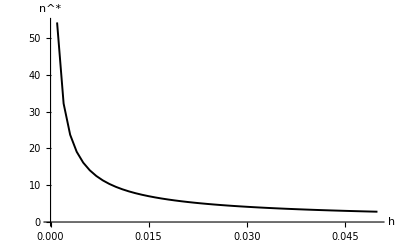

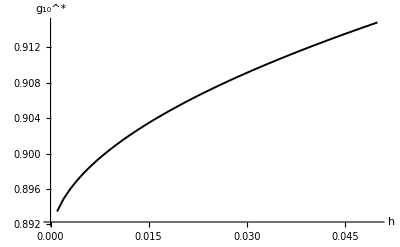

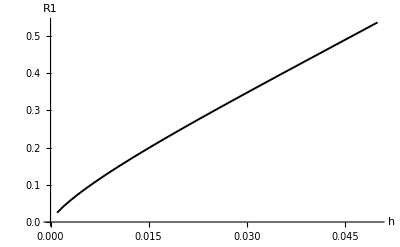

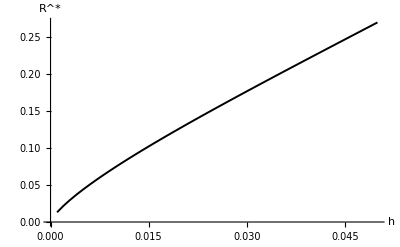

VRdatahtestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdatahtestYZ.xlsx

```mathematica
g1externalh=1.15892+0.01;


RdatahtestYZ=Table[{0,0,0,0,0},{Length[vdatahtestYZ]}];
For[i=1,i<=Length[vdatahtestYZ],i++,Module[{h,g10,n,Rstar},{h,n,g10}=vdatahtestYZ[[i,{1,2,3}]];
R1=vdatahtestYZ[[i,4]];
Rstar=Sqrt[g1externalh-g10]*R1;
RdatahtestYZ[[i]]={h,g10,n,R1,Rstar};
Print[{h,g10,n,R1,Rstar}];]];

VRdatahtestYZ=Select[RdatahtestYZ,#[[2]]>0&];
testhnYZ=ListPlot[VRdatahtestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testhg10YZ=ListPlot[VRdatahtestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhR1YZ=ListLinePlot[VRdatahtestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhRYZ=ListLinePlot[VRdatahtestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatahtestYZ.xlsx",VRdatahtestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatahtestYZ.xlsx",VRdatahtestYZ]
```

### 2.2 Relations of g30 and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;h=1/75;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;g12=1;


samplePoints=Subdivide[0.5,1.5,49];
datag30testYZ=Table[{0,0,0,0,0},{ g30,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, g30=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  g30 = ", g30];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datag30testYZ[[k]]={ g30,n,g10,Sqrt[R12]};
Print[{ g30,n,g10,R12}];
k++;]


vdatag30testYZ=Select[datag30testYZ,#[[2]]>0&&#[[3]]>0&];
Maxg10g30testYZ=Max[vdatag30testYZ[[All,3]]]
```

{1.5,5.64249,0.905568,0.0622414}

{1.47959,5.70163,0.90546,0.0608903}

{1.45918,5.76223,0.905352,0.0595516}

{1.43878,5.82432,0.905243,0.0582252}

{1.41837,5.88798,0.905133,0.0569112}

{1.39796,5.95327,0.905022,0.0556096}

{1.37755,6.02025,0.904911,0.0543204}

{1.35714,6.08899,0.904798,0.0530435}

{1.33673,6.15956,0.904685,0.0517792}

{1.31633,6.23205,0.904571,0.0505273}

{1.29592,6.30654,0.904456,0.0492878}

{1.27551,6.38311,0.904341,0.0480609}

{1.2551,6.46186,0.904224,0.0468465}

{1.23469,6.54288,0.904107,0.0456447}

{1.21429,6.62629,0.903988,0.0444555}

{1.19388,6.71219,0.903869,0.0432789}

{1.17347,6.8007,0.903748,0.042115}

{1.15306,6.89195,0.903627,0.0409637}

{1.13265,6.98608,0.903504,0.0398252}

❌ FindRoot failed at  g30 = 1.11224

{1.09184,7.18354,0.903256,0.0375865}

❌ FindRoot failed at  g30 = 1.07143

{1.05102,7.39439,0.903003,0.0353992}

{1.03061,7.50528,0.902875,0.034325}

❌ FindRoot failed at  g30 = 1.0102

{0.989796,7.73903,0.902615,0.0322155}

❌ FindRoot failed at  g30 = 0.969388

{0.94898,7.9903,0.902349,0.0301584}

{0.928571,8.12317,0.902214,0.0291497}

{0.908163,8.26126,0.902078,0.0281543}

{0.887755,8.40489,0.90194,0.0271722}

{0.867347,8.55443,0.901801,0.0262035}

{0.846939,8.71026,0.90166,0.0252483}

{0.826531,8.87281,0.901517,0.0243067}

❌ FindRoot failed at  g30 = 0.806122

{0.785714,9.22,0.901227,0.0224647}

{0.765306,9.4057,0.901079,0.0215643}

{0.744898,9.60029,0.900929,0.0206779}

{0.72449,9.80445,0.900777,0.0198056}

{0.704082,10.0189,0.900622,0.0189474}

{0.683673,10.2446,0.900466,0.0181035}

{0.663265,10.4824,0.900307,0.017274}

{0.642857,10.7334,0.900146,0.0164591}

{0.622449,10.9987,0.899983,0.0156588}

{0.602041,11.2797,0.899816,0.0148733}

{0.581633,11.5779,0.899647,0.0141028}

{0.561224,11.895,0.899475,0.0133474}

{0.540816,12.233,0.8993,0.0126073}

{0.520408,12.5941,0.899122,0.0118828}

{0.5,12.9809,0.89894,0.011174}

0.905568

#### Graph

{1.5,0.905568,5.64249,0.249482,0.124777}

{1.47959,0.90546,5.70163,0.24676,0.123441}

{1.45918,0.905352,5.76223,0.244032,0.122103}

{1.43878,0.905243,5.82432,0.241299,0.120762}

{1.41837,0.905133,5.88798,0.238561,0.119418}

{1.39796,0.905022,5.95327,0.235817,0.118071}

{1.37755,0.904911,6.02025,0.233067,0.11672}

{1.35714,0.904798,6.08899,0.230312,0.115366}

{1.33673,0.904685,6.15956,0.22755,0.114008}

{1.31633,0.904571,6.23205,0.224783,0.112647}

{1.29592,0.904456,6.30654,0.222009,0.111282}

{1.27551,0.904341,6.38311,0.219228,0.109914}

{1.2551,0.904224,6.46186,0.216441,0.108541}

{1.23469,0.904107,6.54288,0.213646,0.107165}

{1.21429,0.903988,6.62629,0.210845,0.105785}

{1.19388,0.903869,6.71219,0.208036,0.1044}

{1.17347,0.903748,6.8007,0.205219,0.103011}

{1.15306,0.903627,6.89195,0.202395,0.101618}

{1.13265,0.903504,6.98608,0.199563,0.10022}

{1.09184,0.903256,7.18354,0.193872,0.0974108}

{1.05102,0.903003,7.39439,0.188147,0.0945813}

{1.03061,0.902875,7.50528,0.18527,0.0931588}

{0.989796,0.902615,7.73903,0.179487,0.0902973}

{0.94898,0.902349,7.9903,0.173662,0.0874126}

{0.928571,0.902214,8.12317,0.170733,0.0859612}

{0.908163,0.902078,8.26126,0.167792,0.0845034}

{0.887755,0.90194,8.40489,0.16484,0.083039}

{0.867347,0.901801,8.55443,0.161875,0.0815678}

{0.846939,0.90166,8.71026,0.158897,0.0800896}

{0.826531,0.901517,8.87281,0.155906,0.0786041}

{0.785714,0.901227,9.22,0.149882,0.0756101}

{0.765306,0.901079,9.4057,0.146848,0.074101}

{0.744898,0.900929,9.60029,0.143798,0.0725834}

{0.72449,0.900777,9.80445,0.140732,0.0710571}

{0.704082,0.900622,10.0189,0.13765,0.0695216}

{0.683673,0.900466,10.2446,0.134549,0.0679766}

{0.663265,0.900307,10.4824,0.131431,0.0664216}

{0.642857,0.900146,10.7334,0.128293,0.0648563}

{0.622449,0.899983,10.9987,0.125135,0.0632801}

{0.602041,0.899816,11.2797,0.121956,0.0616926}

{0.581633,0.899647,11.5779,0.118755,0.0600932}

{0.561224,0.899475,11.895,0.115531,0.0584813}

{0.540816,0.8993,12.233,0.112282,0.0568564}

{0.520408,0.899122,12.5941,0.109008,0.0552176}

{0.5,0.89894,12.9809,0.105707,0.0535644}

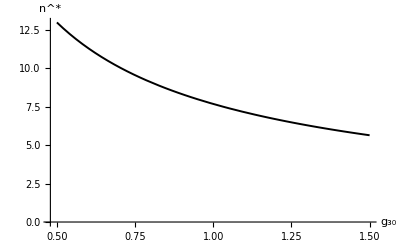

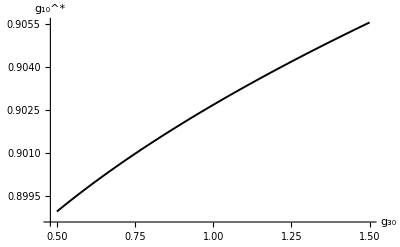

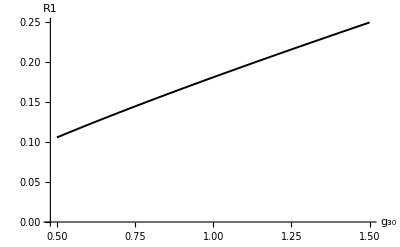

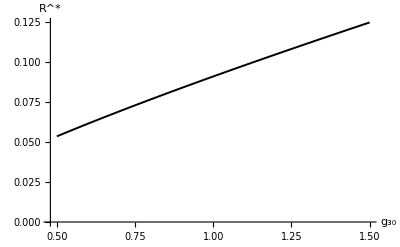

VRdatag30testYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdatag30testYZ.xlsx

```mathematica
g1externalg30=1.14571+0.01;


Rdatag30testYZ=Table[{0,0,0,0,0},{Length[vdatag30testYZ]}];
For[i=1,i<=Length[vdatag30testYZ],i++,Module[{g30,g10,n,Rstar},{g30,n,g10}=vdatag30testYZ[[i,{1,2,3}]];
R1=vdatag30testYZ[[i,4]];
Rstar=Sqrt[g1externalg30-g10]*R1;
Rdatag30testYZ[[i]]={g30,g10,n,R1,Rstar};
Print[{g30,g10,n,R1,Rstar}];]];

VRdatag30testYZ=Select[Rdatag30testYZ,#[[2]]>0&];
testg30nYZ=ListPlot[VRdatag30testYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testg30g10YZ=ListPlot[VRdatag30testYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30R1YZ=ListLinePlot[VRdatag30testYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30RYZ=ListLinePlot[VRdatag30testYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatag30testYZ.xlsx",VRdatag30testYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatag30testYZ.xlsx",VRdatag30testYZ]
```

### 2.3 Relations of KK and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;


samplePoints=E^Subdivide[Log[0.1],Log[0.5],49];
dataKKtestYZ=Table[{0,0,0,0,0},{KK,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.21;
ninit=10.1;

For[i=Length[samplePoints],i>=1,i--,KK=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at KK = ",KK];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataKKtestYZ[[k]]={KK,n,g10,Sqrt[R12]};
Print[{KK,n,g10,R12}];
k++;]


vdataKKtestYZ=Select[dataKKtestYZ,#[[2]]>0&&#[[3]]>0&];
Maxg10KKtestYZ=Max[vdataKKtestYZ[[All,3]]]
```

{0.5,9.5525,0.910183,0.0229526}

{0.483844,9.47906,0.909848,0.0232029}

{0.46821,9.4061,0.909519,0.0234603}

❌ FindRoot failed at KK = 0.453081

{0.438441,9.26159,0.908877,0.0239962}

{0.424274,9.19004,0.908564,0.0242749}

{0.410565,9.11897,0.908256,0.0245607}

{0.397299,9.04837,0.907954,0.0248538}

{0.384461,8.97825,0.907657,0.0251541}

{0.372038,8.90859,0.907365,0.0254618}

{0.360017,8.8394,0.907077,0.0257768}

{0.348384,8.77068,0.906795,0.0260993}

❌ FindRoot failed at KK = 0.337127

{0.326234,8.63464,0.906244,0.0267667}

{0.315693,8.56732,0.905976,0.0271119}

{0.305492,8.50046,0.905712,0.0274647}

{0.295621,8.43406,0.905452,0.0278252}

{0.286069,8.36813,0.905197,0.0281936}

{0.276825,8.30265,0.904947,0.0285699}

{0.26788,8.23763,0.9047,0.0289542}

{0.259225,8.17307,0.904458,0.0293465}

{0.250848,8.10896,0.904219,0.029747}

{0.242743,8.0453,0.903985,0.0301557}

{0.234899,7.98209,0.903754,0.0305727}

{0.227309,7.91933,0.903528,0.0309981}

{0.219965,7.85702,0.903305,0.031432}

{0.212857,7.79516,0.903086,0.0318746}

{0.205979,7.73373,0.90287,0.0323258}

{0.199324,7.67275,0.902658,0.0327858}

{0.192883,7.61221,0.90245,0.0332548}

{0.186651,7.55211,0.902245,0.0337328}

{0.180619,7.49244,0.902044,0.0342199}

{0.174783,7.4332,0.901846,0.0347163}

{0.169136,7.3744,0.901651,0.035222}

{0.163671,7.31603,0.90146,0.0357372}

{0.158382,7.25808,0.901271,0.0362621}

❌ FindRoot failed at KK = 0.153264

{0.148312,7.14346,0.900904,0.0373411}

{0.14352,7.08678,0.900725,0.0378956}

{0.138882,7.03052,0.900549,0.0384602}

{0.134395,6.97467,0.900375,0.039035}

{0.130052,6.91924,0.900205,0.0396203}

{0.12585,6.86422,0.900037,0.0402162}

❌ FindRoot failed at KK = 0.121783

{0.117848,6.75541,0.899711,0.0414402}

❌ FindRoot failed at KK = 0.11404

{0.110356,6.64822,0.899395,0.0427083}

{0.10679,6.59522,0.899241,0.0433593}

{0.103339,6.54263,0.899089,0.0440218}

{0.1,6.49043,0.89894,0.0446959}

0.910183

#### Graph

{0.5,0.910183,9.5525,0.151501,0.0760675}

{0.483844,0.909848,9.47906,0.152325,0.076532}

{0.46821,0.909519,9.4061,0.153167,0.0770055}

{0.438441,0.908877,9.26159,0.154907,0.0779789}

{0.424274,0.908564,9.19004,0.155804,0.0784788}

{0.410565,0.908256,9.11897,0.156719,0.0789873}

{0.397299,0.907954,9.04837,0.157651,0.0795044}

{0.384461,0.907657,8.97825,0.1586,0.0800301}

{0.372038,0.907365,8.90859,0.159567,0.0805642}

{0.360017,0.907077,8.8394,0.160552,0.0811068}

{0.348384,0.906795,8.77068,0.161553,0.0816577}

{0.326234,0.906244,8.63464,0.163605,0.0827843}

{0.315693,0.905976,8.56732,0.164657,0.08336}

{0.305492,0.905712,8.50046,0.165725,0.0839438}

{0.295621,0.905452,8.43406,0.166809,0.0845357}

{0.286069,0.905197,8.36813,0.16791,0.0851357}

{0.276825,0.904947,8.30265,0.169026,0.0857437}

{0.26788,0.9047,8.23763,0.170159,0.0863598}

{0.259225,0.904458,8.17307,0.171308,0.0869838}

{0.250848,0.904219,8.10896,0.172473,0.0876158}

{0.242743,0.903985,8.0453,0.173654,0.0882557}

{0.234899,0.903754,7.98209,0.17485,0.0889034}

{0.227309,0.903528,7.91933,0.176063,0.0895591}

{0.219965,0.903305,7.85702,0.177291,0.0902226}

{0.212857,0.903086,7.79516,0.178534,0.0908939}

{0.205979,0.90287,7.73373,0.179794,0.0915731}

{0.199324,0.902658,7.67275,0.181069,0.09226}

{0.192883,0.90245,7.61221,0.182359,0.0929548}

{0.186651,0.902245,7.55211,0.183665,0.0936573}

{0.180619,0.902044,7.49244,0.184986,0.0943677}

{0.174783,0.901846,7.4332,0.186323,0.0950858}

{0.169136,0.901651,7.3744,0.187675,0.0958117}

{0.163671,0.90146,7.31603,0.189043,0.0965453}

{0.158382,0.901271,7.25808,0.190426,0.0972868}

{0.148312,0.900904,7.14346,0.193238,0.0987931}

{0.14352,0.900725,7.08678,0.194668,0.099558}

{0.138882,0.900549,7.03052,0.196113,0.100331}

{0.134395,0.900375,6.97467,0.197573,0.101111}

{0.130052,0.900205,6.91924,0.199049,0.101899}

{0.12585,0.900037,6.86422,0.20054,0.102696}

{0.117848,0.899711,6.75541,0.203569,0.104312}

{0.110356,0.899395,6.64822,0.20666,0.105959}

{0.10679,0.899241,6.59522,0.208229,0.106795}

{0.103339,0.899089,6.54263,0.209814,0.107639}

{0.1,0.89894,6.49043,0.211414,0.108491}

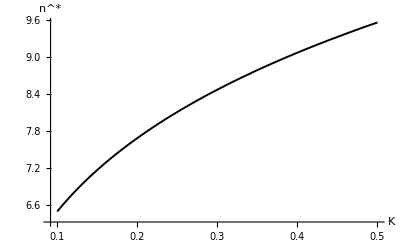

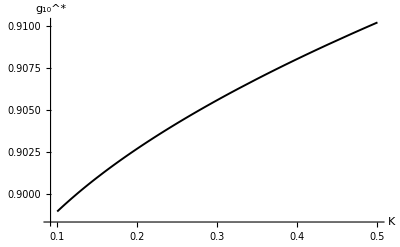

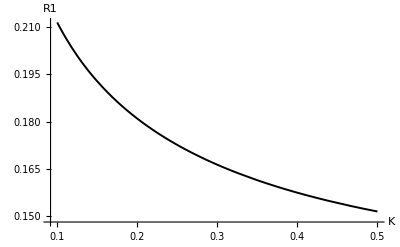

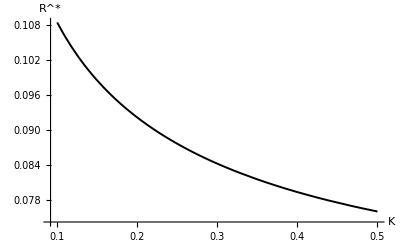

VRdataKKtestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdataKKtestYZ.xlsx

```mathematica
g1externalKK=1.15228+0.01;


RdataKKtestYZ=Table[{0,0,0,0,0},{Length[vdataKKtestYZ]}];
For[i=1,i<=Length[vdataKKtestYZ],i++,Module[{KK,g10,n,Rstar},{KK,n,g10}=vdataKKtestYZ[[i,{1,2,3}]];
R1=vdataKKtestYZ[[i,4]];
Rstar=Sqrt[g1externalKK-g10]*R1;
RdataKKtestYZ[[i]]={KK,g10,n,R1,Rstar};
Print[{KK,g10,n,R1,Rstar}];]];

VRdataKKtestYZ=Select[RdataKKtestYZ,#[[2]]>0&];
testKKnYZ=ListPlot[VRdataKKtestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testKKg10YZ=ListPlot[VRdataKKtestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKR1YZ=ListLinePlot[VRdataKKtestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKRYZ=ListLinePlot[VRdataKKtestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataKKtestYZ.xlsx",VRdataKKtestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdataKKtestYZ.xlsx",VRdataKKtestYZ]
```

## 3. parametric study for skin fiber

### 3.1 Relations of beta and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;h=1.0/75;g12=1;
cf=100;phif=0.05;lamdaf=0.885;


betamin=0;
betamax=Pi/2;
samplePoints=Subdivide[ betamin, betamax,49];
databetatestYZ=Table[{0,0,0,0,0,0},{ beta,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


Guess=1.2;

k=1;

For[i=1,i<=Length[samplePoints],i=i+1,{
beta=samplePoints[[i]];
sol=FindRoot[ OptimalConditionV[g10,beta]==0,{g10,Guess}];
g10=sol[[1,2]];
Guess=g10;
n=1/Pi*√((2*ϕ1)/ϕ2);
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
databetatestYZ[[k]]={beta,n,g10,√R12};
Print[{beta,n,g10,√R12}];
k++;
Clear[g10,n,R12];

}]

vdatabetatestYZ=Select[databetatestYZ,#[[2]]>0&&#[[3]]>0&];
Maxg10betatestYZ=Max[vdatabetatestYZ[[All,3]]]
```

{0,8.49417,1.02191,0.15655}

{π/98,8.4955,1.02129,0.15656}

{π/49,8.49933,1.01945,0.156595}

{(3 π)/98,8.50512,1.01643,0.156663}

{(2 π)/49,8.51208,1.01229,0.156782}

{(5 π)/98,8.51919,1.00713,0.156969}

{(3 π)/49,8.52531,1.00108,0.157243}

{π/14,8.52928,0.994269,0.157621}

{(4 π)/49,8.53002,0.986883,0.158115}

{(9 π)/98,8.52656,0.979101,0.158732}

{(5 π)/49,8.5181,0.97111,0.159475}

{(11 π)/98,8.50401,0.963093,0.160342}

{(6 π)/49,8.48378,0.955222,0.161327}

{(13 π)/98,8.45706,0.947646,0.162425}

{π/7,8.42359,0.940494,0.163626}

{(15 π)/98,8.38321,0.933865,0.164924}

{(8 π)/49,8.33583,0.927837,0.166313}

{(17 π)/98,8.28146,0.922458,0.167785}

{(9 π)/49,8.22019,0.917756,0.169335}

{(19 π)/98,8.15222,0.913737,0.170958}

{(10 π)/49,8.07787,0.91039,0.172648}

{(3 π)/14,7.99757,0.907688,0.174401}

{(11 π)/49,7.91191,0.905592,0.176209}

{(23 π)/98,7.82156,0.904056,0.178068}

{(12 π)/49,7.72733,0.903024,0.179971}

{(25 π)/98,7.63008,0.902441,0.181911}

{(13 π)/49,7.53077,0.902245,0.183882}

{(27 π)/98,7.43034,0.902379,0.185879}

{(2 π)/7,7.32976,0.902786,0.187894}

{(29 π)/98,7.22993,0.903412,0.189921}

{(15 π)/49,7.13171,0.904209,0.191953}

{(31 π)/98,7.03589,0.905133,0.193982}

{(16 π)/49,6.94314,0.906145,0.196001}

{(33 π)/98,6.85406,0.907211,0.198001}

{(17 π)/49,6.76915,0.908302,0.199971}

{(5 π)/14,6.68881,0.909394,0.201901}

{(18 π)/49,6.61337,0.910465,0.20378}

{(37 π)/98,6.54309,0.911501,0.205594}

{(19 π)/49,6.47815,0.912486,0.207331}

{(39 π)/98,6.41869,0.91341,0.208977}

{(20 π)/49,6.36481,0.914264,0.210518}

{(41 π)/98,6.31656,0.915041,0.211942}

{(3 π)/7,6.27399,0.915736,0.213234}

{(43 π)/98,6.23711,0.916345,0.214382}

{(22 π)/49,6.20592,0.916865,0.215375}

{(45 π)/98,6.18042,0.917292,0.216203}

{(23 π)/49,6.1606,0.917626,0.216856}

{(47 π)/98,6.14646,0.917866,0.217328}

{(24 π)/49,6.13797,0.91801,0.217613}

{π/2,6.13514,0.918058,0.217709}

1.02191

#### Graph

{0,1.02191,8.49417,0.15655,0.0563771}

{π/98,1.02129,8.4955,0.15656,0.0565149}

{π/49,1.01945,8.49933,0.156595,0.0569249}

{(3 π)/98,1.01643,8.50512,0.156663,0.0575976}

{(2 π)/49,1.01229,8.51208,0.156782,0.058517}

{(5 π)/98,1.00713,8.51919,0.156969,0.0596619}

{(3 π)/49,1.00108,8.52531,0.157243,0.0610063}

{π/14,0.994269,8.52928,0.157621,0.0625202}

{(4 π)/49,0.986883,8.53002,0.158115,0.0641714}

{(9 π)/98,0.979101,8.52656,0.158732,0.0659262}

{(5 π)/49,0.97111,8.5181,0.159475,0.0677516}

{(11 π)/98,0.963093,8.50401,0.160342,0.0696162}

{(6 π)/49,0.955222,8.48378,0.161327,0.0714916}

{(13 π)/98,0.947646,8.45706,0.162425,0.073353}

{π/7,0.940494,8.42359,0.163626,0.0751801}

{(15 π)/98,0.933865,8.38321,0.164924,0.076957}

{(8 π)/49,0.927837,8.33583,0.166313,0.0786718}

{(17 π)/98,0.922458,8.28146,0.167785,0.0803164}

{(9 π)/49,0.917756,8.22019,0.169335,0.0818859}

{(19 π)/98,0.913737,8.15222,0.170958,0.0833781}

{(10 π)/49,0.91039,8.07787,0.172648,0.084793}

{(3 π)/14,0.907688,7.99757,0.174401,0.0861321}

{(11 π)/49,0.905592,7.91191,0.176209,0.0873983}

{(23 π)/98,0.904056,7.82156,0.178068,0.0885956}

{(12 π)/49,0.903024,7.72733,0.179971,0.0897286}

{(25 π)/98,0.902441,7.63008,0.181911,0.0908024}

{(13 π)/49,0.902245,7.53077,0.183882,0.0918225}

{(27 π)/98,0.902379,7.43034,0.185879,0.0927945}

{(2 π)/7,0.902786,7.32976,0.187894,0.0937238}

{(29 π)/98,0.903412,7.22993,0.189921,0.0946155}

{(15 π)/49,0.904209,7.13171,0.191953,0.0954741}

{(31 π)/98,0.905133,7.03589,0.193982,0.0963032}

{(16 π)/49,0.906145,6.94314,0.196001,0.0971056}

{(33 π)/98,0.907211,6.85406,0.198001,0.0978831}

{(17 π)/49,0.908302,6.76915,0.199971,0.0986362}

{(5 π)/14,0.909394,6.68881,0.201901,0.0993647}

{(18 π)/49,0.910465,6.61337,0.20378,0.100067}

{(37 π)/98,0.911501,6.54309,0.205594,0.100741}

{(19 π)/49,0.912486,6.47815,0.207331,0.101383}

{(39 π)/98,0.91341,6.41869,0.208977,0.101991}

{(20 π)/49,0.914264,6.36481,0.210518,0.102558}

{(41 π)/98,0.915041,6.31656,0.211942,0.103083}

{(3 π)/7,0.915736,6.27399,0.213234,0.103559}

{(43 π)/98,0.916345,6.23711,0.214382,0.103982}

{(22 π)/49,0.916865,6.20592,0.215375,0.104348}

{(45 π)/98,0.917292,6.18042,0.216203,0.104654}

{(23 π)/49,0.917626,6.1606,0.216856,0.104895}

{(47 π)/98,0.917866,6.14646,0.217328,0.10507}

{(24 π)/49,0.91801,6.13797,0.217613,0.105175}

{π/2,0.918058,6.13514,0.217709,0.10521}

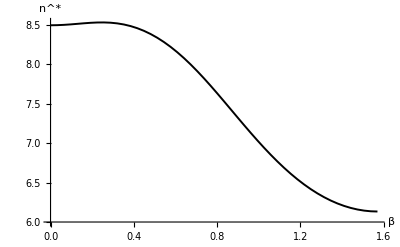

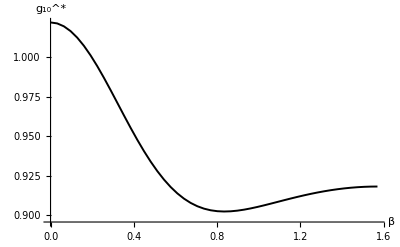

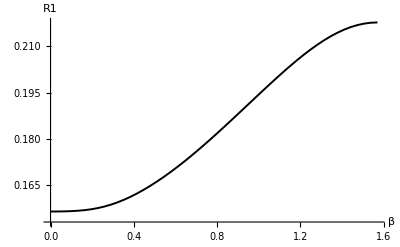

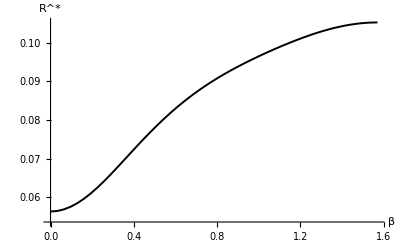

VRdatabetatestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdatabetatestYZ.xlsx

```mathematica
g1externalbeta=1.1416+0.01;


RdatabetatestYZ=Table[{0,0,0,0,0},{Length[vdatabetatestYZ]}];
For[i=1,i<=Length[vdatabetatestYZ],i++,Module[{beta,g10,n,Rstar},{beta,n,g10}=vdatabetatestYZ[[i,{1,2,3}]];
R1=vdatabetatestYZ[[i,4]];
Rstar=Sqrt[g1externalbeta-g10]*R1;
RdatabetatestYZ[[i]]={beta,g10,n,R1,Rstar};
Print[{beta,g10,n,R1,Rstar}];]];

VRdatabetatestYZ=Select[RdatabetatestYZ,#[[2]]>0&];
testbetanYZ=ListPlot[VRdatabetatestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testbetag10YZ=ListPlot[VRdatabetatestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaR1YZ=ListLinePlot[VRdatabetatestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaRYZ=ListLinePlot[VRdatabetatestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatabetatestYZ.xlsx",VRdatabetatestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatabetatestYZ.xlsx",VRdatabetatestYZ]
```

### 3.2 Relations of lamdaf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;KK=0.2;g12=1;
cf=100;phif=0.05;beta=Pi/4;


samplePoints=Subdivide[0.1,1,50];

datalamdaftestYZ=Table[{0,0,0,0,0},{ lamdaf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, lamdaf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  lamdaf = ", lamdaf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datalamdaftestYZ[[k]]={ lamdaf,n,g10,Sqrt[R12]};
Print[{ lamdaf,n,g10,R12}];
k++;]


vdatalamdaftestYZ=Select[datalamdaftestYZ,#[[2]]>0&&#[[3]]>0&];
MaxlamdaftestYZ=Max[vdatalamdaftestYZ[[All,3]]]
```

{1.,6.8283,1.01435,0.0361535}

{0.982,6.98287,0.994171,0.0354542}

❌ FindRoot failed at  lamdaf = 0.964

{0.946,7.26874,0.956879,0.0342655}

{0.928,7.39949,0.939742,0.0337576}

{0.91,7.52205,0.923579,0.0332994}

{0.892,7.63659,0.908355,0.0328869}

{0.874,7.74338,0.894031,0.0325164}

{0.856,7.84276,0.880563,0.0321848}

{0.838,7.93515,0.867906,0.0318889}

{0.82,8.02097,0.856014,0.0316256}

{0.802,8.10067,0.84484,0.0313921}

{0.784,8.17469,0.834339,0.0311854}

{0.766,8.24346,0.82447,0.0310029}

{0.748,8.30739,0.815189,0.030842}

{0.73,8.36686,0.806459,0.0307006}

{0.712,8.42223,0.798244,0.0305763}

{0.694,8.47382,0.790509,0.0304674}

{0.676,8.52193,0.783223,0.0303721}

{0.658,8.56683,0.776357,0.0302888}

{0.64,8.60879,0.769885,0.0302161}

{0.622,8.64802,0.76378,0.0301529}

{0.604,8.68474,0.75802,0.0300979}

{0.586,8.71912,0.752585,0.0300502}

{0.568,8.75134,0.747455,0.030009}

{0.55,8.78154,0.742613,0.0299735}

{0.532,8.80988,0.738041,0.0299429}

{0.514,8.83647,0.733726,0.0299168}

{0.496,8.86142,0.729653,0.0298945}

{0.478,8.88484,0.725809,0.0298756}

{0.46,8.90683,0.722184,0.0298596}

{0.442,8.92746,0.718766,0.0298463}

{0.424,8.94682,0.715546,0.0298352}

{0.406,8.96497,0.712514,0.0298261}

❌ FindRoot failed at  lamdaf = 0.388

{0.37,8.9979,0.706985,0.0298128}

❌ FindRoot failed at  lamdaf = 0.352

{0.334,9.02668,0.702119,0.0298046}

{0.316,9.03964,0.699919,0.029802}

{0.298,9.0517,0.697868,0.0298002}

{0.28,9.06289,0.695959,0.029799}

{0.262,9.07324,0.69419,0.0297983}

{0.244,9.08278,0.692555,0.0297981}

{0.226,9.09155,0.69105,0.0297982}

{0.208,9.09956,0.689673,0.0297986}

{0.19,9.10684,0.688421,0.0297992}

{0.172,9.1134,0.68729,0.0297999}

{0.154,9.11926,0.686279,0.0298007}

{0.136,9.12444,0.685384,0.0298015}

{0.118,9.12895,0.684605,0.0298023}

{0.1,9.13279,0.683939,0.029803}

1.01435

#### Graph

{1.,1.01435,6.8283,0.190141,0.134381}

{0.982,0.994171,6.98287,0.188293,0.135737}

{0.946,0.956879,7.26874,0.18511,0.138147}

{0.928,0.939742,7.39949,0.183732,0.139213}

{0.91,0.923579,7.52205,0.182481,0.140198}

{0.892,0.908355,7.63659,0.181347,0.141112}

{0.874,0.894031,7.74338,0.180323,0.141965}

{0.856,0.880563,7.84276,0.179401,0.142765}

{0.838,0.867906,7.93515,0.178575,0.14352}

{0.82,0.856014,8.02097,0.177836,0.144236}

{0.802,0.84484,8.10067,0.177178,0.144918}

{0.784,0.834339,8.17469,0.176594,0.145569}

{0.766,0.82447,8.24346,0.176076,0.146193}

{0.748,0.815189,8.30739,0.175619,0.146792}

{0.73,0.806459,8.36686,0.175216,0.147367}

{0.712,0.798244,8.42223,0.174861,0.14792}

{0.694,0.790509,8.47382,0.174549,0.148452}

{0.676,0.783223,8.52193,0.174276,0.148964}

{0.658,0.776357,8.56683,0.174037,0.149457}

{0.64,0.769885,8.60879,0.173828,0.149932}

{0.622,0.76378,8.64802,0.173646,0.150388}

{0.604,0.75802,8.68474,0.173487,0.150826}

{0.586,0.752585,8.71912,0.17335,0.151248}

{0.568,0.747455,8.75134,0.173231,0.151652}

{0.55,0.742613,8.78154,0.173128,0.152041}

{0.532,0.738041,8.80988,0.17304,0.152413}

{0.514,0.733726,8.83647,0.172965,0.152769}

{0.496,0.729653,8.86142,0.1729,0.153111}

{0.478,0.725809,8.88484,0.172846,0.153437}

{0.46,0.722184,8.90683,0.172799,0.153748}

{0.442,0.718766,8.92746,0.172761,0.154045}

{0.424,0.715546,8.94682,0.172729,0.154328}

{0.406,0.712514,8.96497,0.172702,0.154598}

{0.37,0.706985,8.9979,0.172664,0.155096}

{0.334,0.702119,9.02668,0.17264,0.155541}

{0.316,0.699919,9.03964,0.172633,0.155745}

{0.298,0.697868,9.0517,0.172627,0.155936}

{0.28,0.695959,9.06289,0.172624,0.156115}

{0.262,0.69419,9.07324,0.172622,0.156282}

{0.244,0.692555,9.08278,0.172621,0.156438}

{0.226,0.69105,9.09155,0.172622,0.156581}

{0.208,0.689673,9.09956,0.172623,0.156713}

{0.19,0.688421,9.10684,0.172624,0.156834}

{0.172,0.68729,9.1134,0.172626,0.156943}

{0.154,0.686279,9.11926,0.172629,0.157041}

{0.136,0.685384,9.12444,0.172631,0.157128}

{0.118,0.684605,9.12895,0.172633,0.157204}

{0.1,0.683939,9.13279,0.172636,0.157269}

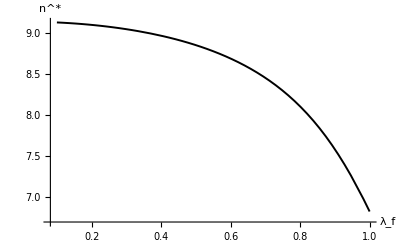

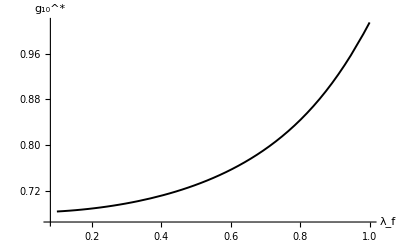

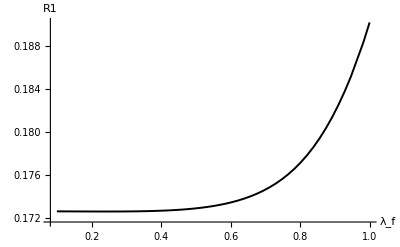

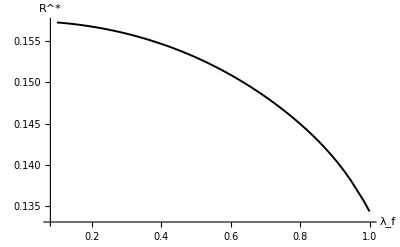

VRdatalamdaftestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdatalamdaftestYZ.xlsx

```mathematica
g1externallamdaf=1.50384+0.01;


RdatalamdaftestYZ=Table[{0,0,0,0,0},{Length[vdatalamdaftestYZ]}];
For[i=1,i<=Length[vdatalamdaftestYZ],i++,Module[{lamdaf,g10,n,Rstar},{lamdaf,n,g10}=vdatalamdaftestYZ[[i,{1,2,3}]];
R1=vdatalamdaftestYZ[[i,4]];
Rstar=Sqrt[g1externallamdaf-g10]*R1;
RdatalamdaftestYZ[[i]]={lamdaf,g10,n,R1,Rstar};
Print[{lamdaf,g10,n,R1,Rstar}];]];

VRdatalamdaftestYZ=Select[RdatalamdaftestYZ,#[[2]]>0&];
testlamdafnYZ=ListPlot[VRdatalamdaftestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testlamdafg10YZ=ListPlot[VRdatalamdaftestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafR1YZ=ListLinePlot[VRdatalamdaftestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafRYZ=ListLinePlot[VRdatalamdaftestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatalamdaftestYZ.xlsx",VRdatalamdaftestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatalamdaftestYZ.xlsx",VRdatalamdaftestYZ]
```

### 3.3 Relations of cf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
phif=0.05;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[50,100,100];
datacftestYZ=Table[{0,0,0,0,0},{ cf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, cf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  cf = ", cf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datacftestYZ[[k]]={ cf,n,g10,Sqrt[R12]};
Print[{ cf,n,g10,R12}];
k++;]


vdatacftestYZ=Select[datacftestYZ,#[[2]]>0&&#[[3]]>0&];
MaxcftestYZ=Max[vdatacftestYZ[[All,3]]]
```

{100,7.67902,0.90268,0.032738}

{199/2,7.68099,0.902949,0.0327169}

{99,7.68296,0.903219,0.0326958}

{197/2,7.68494,0.90349,0.0326747}

{98,7.68693,0.903762,0.0326535}

{195/2,7.68892,0.904036,0.0326322}

{97,7.69092,0.904311,0.0326108}

{193/2,7.69293,0.904587,0.0325894}

{96,7.69494,0.904865,0.0325679}

{191/2,7.69696,0.905144,0.0325464}

{95,7.69899,0.905425,0.0325247}

{189/2,7.70103,0.905707,0.032503}

{94,7.70307,0.90599,0.0324813}

{187/2,7.70512,0.906275,0.0324595}

{93,7.70718,0.906561,0.0324376}

{185/2,7.70924,0.906848,0.0324156}

{92,7.71132,0.907137,0.0323936}

{183/2,7.7134,0.907428,0.0323715}

{91,7.71548,0.907719,0.0323493}

{181/2,7.71758,0.908013,0.032327}

{90,7.71968,0.908308,0.0323047}

{179/2,7.7218,0.908604,0.0322823}

{89,7.72392,0.908902,0.0322598}

{177/2,7.72604,0.909201,0.0322373}

{88,7.72818,0.909502,0.0322147}

{175/2,7.73032,0.909805,0.0321919}

{87,7.73248,0.910109,0.0321692}

{173/2,7.73464,0.910414,0.0321463}

{86,7.73681,0.910722,0.0321234}

{171/2,7.73899,0.91103,0.0321003}

{85,7.74117,0.911341,0.0320772}

{169/2,7.74337,0.911653,0.032054}

{84,7.74557,0.911967,0.0320308}

{167/2,7.74779,0.912282,0.0320074}

{83,7.75001,0.9126,0.031984}

{165/2,7.75224,0.912919,0.0319605}

{82,7.75448,0.913239,0.0319369}

{163/2,7.75673,0.913562,0.0319132}

{81,7.75899,0.913886,0.0318894}

{161/2,7.76126,0.914212,0.0318655}

{80,7.76354,0.91454,0.0318415}

{159/2,7.76583,0.914869,0.0318175}

{79,7.76813,0.9152,0.0317933}

{157/2,7.77044,0.915534,0.0317691}

{78,7.77276,0.915869,0.0317448}

{155/2,7.77509,0.916206,0.0317203}

{77,7.77743,0.916545,0.0316958}

{153/2,7.77978,0.916886,0.0316712}

{76,7.78214,0.917228,0.0316464}

{151/2,7.78451,0.917573,0.0316216}

{75,7.78689,0.91792,0.0315967}

{149/2,7.78929,0.918269,0.0315717}

{74,7.79169,0.918619,0.0315465}

{147/2,7.79411,0.918972,0.0315213}

{73,7.79653,0.919327,0.031496}

{145/2,7.79897,0.919684,0.0314705}

{72,7.80142,0.920043,0.031445}

{143/2,7.80388,0.920404,0.0314193}

{71,7.80635,0.920768,0.0313935}

{141/2,7.80884,0.921133,0.0313676}

{70,7.81134,0.921501,0.0313416}

{139/2,7.81385,0.921871,0.0313155}

{69,7.81637,0.922243,0.0312893}

{137/2,7.8189,0.922618,0.031263}

{68,7.82145,0.922995,0.0312365}

{135/2,7.82401,0.923374,0.0312099}

{67,7.82658,0.923755,0.0311832}

{133/2,7.82917,0.924139,0.0311564}

{66,7.83177,0.924526,0.0311294}

{131/2,7.83439,0.924914,0.0311023}

{65,7.83701,0.925306,0.0310751}

{129/2,7.83965,0.925699,0.0310478}

{64,7.84231,0.926096,0.0310203}

{127/2,7.84498,0.926494,0.0309927}

{63,7.84766,0.926896,0.0309649}

{125/2,7.85036,0.9273,0.030937}

{62,7.85308,0.927706,0.030909}

{123/2,7.85581,0.928115,0.0308809}

{61,7.85855,0.928527,0.0308526}

{121/2,7.86131,0.928942,0.0308241}

{60,7.86409,0.92936,0.0307955}

{119/2,7.86688,0.92978,0.0307668}

{59,7.86969,0.930203,0.0307379}

{117/2,7.87251,0.930629,0.0307088}

{58,7.87535,0.931058,0.0306796}

{115/2,7.87821,0.931489,0.0306503}

{57,7.88108,0.931924,0.0306207}

{113/2,7.88398,0.932362,0.0305911}

{56,7.88688,0.932803,0.0305612}

{111/2,7.88981,0.933247,0.0305312}

{55,7.89276,0.933694,0.030501}

{109/2,7.89572,0.934144,0.0304707}

{54,7.89871,0.934597,0.0304401}

{107/2,7.90171,0.935054,0.0304094}

{53,7.90473,0.935514,0.0303786}

{105/2,7.90777,0.935977,0.0303475}

{52,7.91083,0.936444,0.0303162}

{103/2,7.91391,0.936914,0.0302848}

{51,7.91701,0.937387,0.0302532}

{101/2,7.92013,0.937864,0.0302213}

{50,7.92328,0.938345,0.0301893}

0.938345

#### Graph

{100,0.90268,7.67902,0.180936,0.0902726}

{199/2,0.902949,7.68099,0.180878,0.0901948}

{99,0.903219,7.68296,0.18082,0.0901168}

{197/2,0.90349,7.68494,0.180761,0.0900385}

{98,0.903762,7.68693,0.180703,0.0899598}

{195/2,0.904036,7.68892,0.180644,0.0898808}

{97,0.904311,7.69092,0.180585,0.0898014}

{193/2,0.904587,7.69293,0.180525,0.0897217}

{96,0.904865,7.69494,0.180466,0.0896417}

{191/2,0.905144,7.69696,0.180406,0.0895613}

{95,0.905425,7.69899,0.180346,0.0894806}

{189/2,0.905707,7.70103,0.180286,0.0893996}

{94,0.90599,7.70307,0.180226,0.0893181}

{187/2,0.906275,7.70512,0.180165,0.0892364}

{93,0.906561,7.70718,0.180104,0.0891543}

{185/2,0.906848,7.70924,0.180043,0.0890718}

{92,0.907137,7.71132,0.179982,0.0889889}

{183/2,0.907428,7.7134,0.179921,0.0889057}

{91,0.907719,7.71548,0.179859,0.0888221}

{181/2,0.908013,7.71758,0.179797,0.0887381}

{90,0.908308,7.71968,0.179735,0.0886538}

{179/2,0.908604,7.7218,0.179673,0.088569}

{89,0.908902,7.72392,0.17961,0.0884839}

{177/2,0.909201,7.72604,0.179547,0.0883984}

{88,0.909502,7.72818,0.179484,0.0883125}

{175/2,0.909805,7.73032,0.179421,0.0882262}

{87,0.910109,7.73248,0.179358,0.0881395}

{173/2,0.910414,7.73464,0.179294,0.0880524}

{86,0.910722,7.73681,0.17923,0.0879649}

{171/2,0.91103,7.73899,0.179166,0.087877}

{85,0.911341,7.74117,0.179101,0.0877886}

{169/2,0.911653,7.74337,0.179036,0.0876999}

{84,0.911967,7.74557,0.178971,0.0876107}

{167/2,0.912282,7.74779,0.178906,0.0875211}

{83,0.9126,7.75001,0.178841,0.087431}

{165/2,0.912919,7.75224,0.178775,0.0873405}

{82,0.913239,7.75448,0.178709,0.0872496}

{163/2,0.913562,7.75673,0.178643,0.0871582}

{81,0.913886,7.75899,0.178576,0.0870664}

{161/2,0.914212,7.76126,0.178509,0.0869741}

{80,0.91454,7.76354,0.178442,0.0868814}

{159/2,0.914869,7.76583,0.178375,0.0867881}

{79,0.9152,7.76813,0.178307,0.0866945}

{157/2,0.915534,7.77044,0.178239,0.0866003}

{78,0.915869,7.77276,0.178171,0.0865057}

{155/2,0.916206,7.77509,0.178102,0.0864105}

{77,0.916545,7.77743,0.178033,0.0863149}

{153/2,0.916886,7.77978,0.177964,0.0862188}

{76,0.917228,7.78214,0.177894,0.0861222}

{151/2,0.917573,7.78451,0.177825,0.086025}

{75,0.91792,7.78689,0.177755,0.0859274}

{149/2,0.918269,7.78929,0.177684,0.0858293}

{74,0.918619,7.79169,0.177613,0.0857306}

{147/2,0.918972,7.79411,0.177542,0.0856314}

{73,0.919327,7.79653,0.177471,0.0855316}

{145/2,0.919684,7.79897,0.177399,0.0854313}

{72,0.920043,7.80142,0.177327,0.0853305}

{143/2,0.920404,7.80388,0.177255,0.0852291}

{71,0.920768,7.80635,0.177182,0.0851272}

{141/2,0.921133,7.80884,0.177109,0.0850247}

{70,0.921501,7.81134,0.177036,0.0849216}

{139/2,0.921871,7.81385,0.176962,0.0848179}

{69,0.922243,7.81637,0.176888,0.0847137}

{137/2,0.922618,7.8189,0.176813,0.0846088}

{68,0.922995,7.82145,0.176738,0.0845034}

{135/2,0.923374,7.82401,0.176663,0.0843973}

{67,0.923755,7.82658,0.176588,0.0842907}

{133/2,0.924139,7.82917,0.176512,0.0841834}

{66,0.924526,7.83177,0.176435,0.0840755}

{131/2,0.924914,7.83439,0.176358,0.0839669}

{65,0.925306,7.83701,0.176281,0.0838577}

{129/2,0.925699,7.83965,0.176204,0.0837479}

{64,0.926096,7.84231,0.176126,0.0836374}

{127/2,0.926494,7.84498,0.176047,0.0835262}

{63,0.926896,7.84766,0.175969,0.0834143}

{125/2,0.9273,7.85036,0.175889,0.0833018}

{62,0.927706,7.85308,0.17581,0.0831886}

{123/2,0.928115,7.85581,0.17573,0.0830746}

{61,0.928527,7.85855,0.175649,0.08296}

{121/2,0.928942,7.86131,0.175568,0.0828446}

{60,0.92936,7.86409,0.175487,0.0827285}

{119/2,0.92978,7.86688,0.175405,0.0826117}

{59,0.930203,7.86969,0.175322,0.0824941}

{117/2,0.930629,7.87251,0.175239,0.0823758}

{58,0.931058,7.87535,0.175156,0.0822567}

{115/2,0.931489,7.87821,0.175072,0.0821368}

{57,0.931924,7.88108,0.174988,0.0820161}

{113/2,0.932362,7.88398,0.174903,0.0818946}

{56,0.932803,7.88688,0.174818,0.0817723}

{111/2,0.933247,7.88981,0.174732,0.0816492}

{55,0.933694,7.89276,0.174645,0.0815253}

{109/2,0.934144,7.89572,0.174559,0.0814005}

{54,0.934597,7.89871,0.174471,0.0812748}

{107/2,0.935054,7.90171,0.174383,0.0811483}

{53,0.935514,7.90473,0.174294,0.0810209}

{105/2,0.935977,7.90777,0.174205,0.0808926}

{52,0.936444,7.91083,0.174116,0.0807634}

{103/2,0.936914,7.91391,0.174025,0.0806333}

{51,0.937387,7.91701,0.173934,0.0805023}

{101/2,0.937864,7.92013,0.173843,0.0803703}

{50,0.938345,7.92328,0.173751,0.0802373}

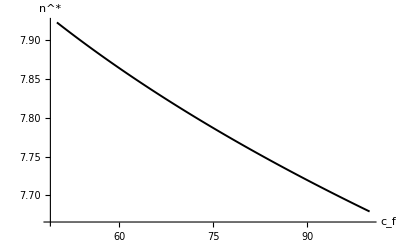

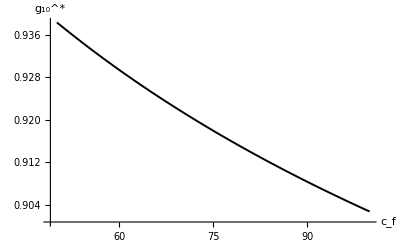

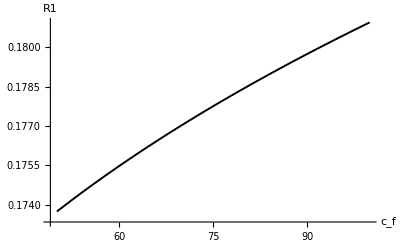

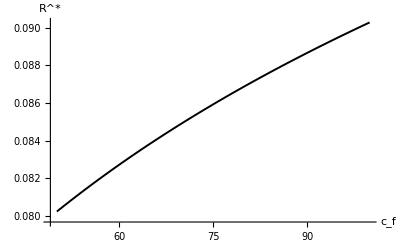

VRdatacftestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdatacftestYZ.xlsx

```mathematica
g1externalcf=1.1416+0.01;


RdatacftestYZ=Table[{0,0,0,0,0},{Length[vdatacftestYZ]}];
For[i=1,i<=Length[vdatacftestYZ],i++,Module[{cf,g10,n,Rstar},{cf,n,g10}=vdatacftestYZ[[i,{1,2,3}]];
R1=vdatacftestYZ[[i,4]];
Rstar=Sqrt[g1externalcf-g10]*R1;
RdatacftestYZ[[i]]={cf,g10,n,R1,Rstar};
Print[{cf,g10,n,R1,Rstar}];]];

VRdatacftestYZ=Select[RdatacftestYZ,#[[2]]>0&];
testcfnYZ=ListPlot[VRdatacftestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testcfg10YZ=ListPlot[VRdatacftestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfR1YZ=ListLinePlot[VRdatacftestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfRYZ=ListLinePlot[VRdatacftestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatacftestYZ.xlsx",VRdatacftestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatacftestYZ.xlsx",VRdatacftestYZ]
```

### 3.4 Relations of phif and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
cf=100;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[0,0.1,50];
dataphiftestYZ=Table[{0,0,0,0,0},{ phif,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, phif=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  phif = ", phif];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataphiftestYZ[[k]]={ phif,n,g10,Sqrt[R12]};
Print[{ phif,n,g10,R12}];
k++;]


vdataphiftestYZ=Select[dataphiftestYZ,#[[2]]>0&&#[[3]]>0&];
MaxphiftestYZ=Max[vdataphiftestYZ[[All,3]]]
```

{0.1,7.44113,0.863104,0.0355745}

{0.098,7.44867,0.864258,0.0354828}

{0.096,7.45633,0.865436,0.0353898}

{0.094,7.46411,0.866641,0.0352956}

{0.092,7.47201,0.867872,0.0351999}

{0.09,7.48003,0.869132,0.0351029}

{0.088,7.48819,0.87042,0.0350044}

{0.086,7.49648,0.871739,0.0349043}

{0.084,7.50491,0.87309,0.0348027}

{0.082,7.5135,0.874474,0.0346993}

{0.08,7.52224,0.875892,0.0345943}

{0.078,7.53115,0.877346,0.0344874}

{0.076,7.54023,0.878838,0.0343786}

{0.074,7.54949,0.880369,0.0342678}

{0.072,7.55894,0.881941,0.0341549}

{0.07,7.56859,0.883557,0.0340398}

{0.068,7.57845,0.885219,0.0339224}

{0.066,7.58853,0.886928,0.0338026}

{0.064,7.59885,0.888688,0.0336802}

{0.062,7.60942,0.890501,0.0335552}

{0.06,7.62025,0.89237,0.0334272}

{0.058,7.63137,0.894299,0.0332962}

{0.056,7.64278,0.89629,0.033162}

{0.054,7.65451,0.898348,0.0330244}

{0.052,7.66658,0.900476,0.0328831}

{0.05,7.67902,0.90268,0.032738}

{0.048,7.69186,0.904964,0.0325887}

{0.046,7.70511,0.907333,0.0324349}

{0.044,7.71883,0.909795,0.0322763}

{0.042,7.73303,0.912354,0.0321125}

{0.04,7.74778,0.915019,0.0319432}

{0.038,7.76312,0.917797,0.0317677}

{0.036,7.7791,0.920699,0.0315856}

{0.034,7.79578,0.923734,0.0313962}

{0.032,7.81325,0.926914,0.0311988}

{0.03,7.83159,0.930252,0.0309925}

{0.028,7.85089,0.933764,0.0307764}

{0.026,7.87127,0.937467,0.0305494}

{0.024,7.89288,0.94138,0.03031}

{0.022,7.91587,0.945528,0.0300565}

{0.02,7.94046,0.949938,0.0297871}

{0.018,7.96689,0.954642,0.0294991}

{0.016,7.99546,0.95968,0.0291896}

{0.014,8.02656,0.965099,0.0288545}

{0.012,8.06069,0.970957,0.028489}

{0.01,8.0985,0.977327,0.0280863}

{0.008,8.14084,0.984301,0.0276375}

{0.006,8.18891,0.991998,0.0271301}

{0.004,8.24438,1.00058,0.0265462}

{0.002,8.30975,1.01026,0.0258589}

{0.,8.38891,1.02135,0.0250261}

1.02135

#### Graph

{0.1,0.863104,7.44113,0.188612,0.109428}

{0.098,0.864258,7.44867,0.188369,0.1091}

{0.096,0.865436,7.45633,0.188122,0.108765}

{0.094,0.866641,7.46411,0.187871,0.108424}

{0.092,0.867872,7.47201,0.187616,0.108077}

{0.09,0.869132,7.48003,0.187358,0.107723}

{0.088,0.87042,7.48819,0.187095,0.107362}

{0.086,0.871739,7.49648,0.186827,0.106993}

{0.084,0.87309,7.50491,0.186555,0.106617}

{0.082,0.874474,7.5135,0.186278,0.106233}

{0.08,0.875892,7.52224,0.185995,0.105841}

{0.078,0.877346,7.53115,0.185708,0.10544}

{0.076,0.878838,7.54023,0.185415,0.105029}

{0.074,0.880369,7.54949,0.185116,0.104609}

{0.072,0.881941,7.55894,0.18481,0.104179}

{0.07,0.883557,7.56859,0.184499,0.103739}

{0.068,0.885219,7.57845,0.18418,0.103288}

{0.066,0.886928,7.58853,0.183855,0.102824}

{0.064,0.888688,7.59885,0.183522,0.102349}

{0.062,0.890501,7.60942,0.183181,0.10186}

{0.06,0.89237,7.62025,0.182831,0.101358}

{0.058,0.894299,7.63137,0.182473,0.100842}

{0.056,0.89629,7.64278,0.182104,0.10031}

{0.054,0.898348,7.65451,0.181726,0.0997612}

{0.052,0.900476,7.66658,0.181337,0.0991954}

{0.05,0.90268,7.67902,0.180936,0.0986111}

{0.048,0.904964,7.69186,0.180523,0.098007}

{0.046,0.907333,7.70511,0.180097,0.0973817}

{0.044,0.909795,7.71883,0.179656,0.0967337}

{0.042,0.912354,7.73303,0.1792,0.0960611}

{0.04,0.915019,7.74778,0.178727,0.0953622}

{0.038,0.917797,7.76312,0.178235,0.0946347}

{0.036,0.920699,7.7791,0.177723,0.0938761}

{0.034,0.923734,7.79578,0.17719,0.0930838}

{0.032,0.926914,7.81325,0.176632,0.0922546}

{0.03,0.930252,7.83159,0.176047,0.0913848}

{0.028,0.933764,7.85089,0.175432,0.0904703}

{0.026,0.937467,7.87127,0.174784,0.0895063}

{0.024,0.94138,7.89288,0.174098,0.0884871}

{0.022,0.945528,7.91587,0.173368,0.0874061}

{0.02,0.949938,7.94046,0.172589,0.0862553}

{0.018,0.954642,7.96689,0.171753,0.0850251}

{0.016,0.95968,7.99546,0.17085,0.083704}

{0.014,0.965099,8.02656,0.169866,0.0822775}

{0.012,0.970957,8.06069,0.168787,0.0807275}

{0.01,0.977327,8.0985,0.16759,0.0790311}

{0.008,0.984301,8.14084,0.166245,0.0771581}

{0.006,0.991998,8.18891,0.164712,0.0750684}

{0.004,1.00058,8.24438,0.16293,0.0727065}

{0.002,1.01026,8.30975,0.160807,0.0699933}

{0.,1.02135,8.38891,0.158196,0.0668107}

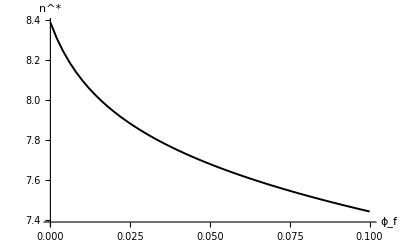

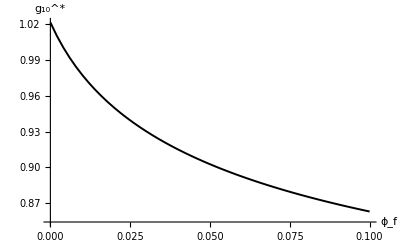

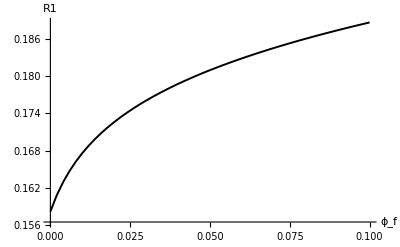

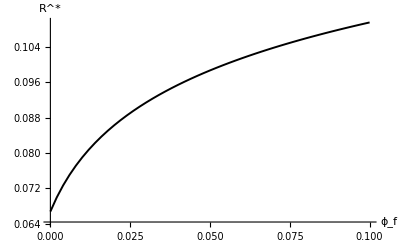

VRdataphiftestYZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.3 YZ_data\VRdataphiftestYZ.xlsx

```mathematica
g1externalphif=1.18971+0.01;


RdataphiftestYZ=Table[{0,0,0,0,0},{Length[vdataphiftestYZ]}];
For[i=1,i<=Length[vdataphiftestYZ],i++,Module[{phif,g10,n,Rstar},{phif,n,g10}=vdataphiftestYZ[[i,{1,2,3}]];
R1=vdataphiftestYZ[[i,4]];
Rstar=Sqrt[g1externalphif-g10]*R1;
RdataphiftestYZ[[i]]={phif,g10,n,R1,Rstar};
Print[{phif,g10,n,R1,Rstar}];]];

VRdataphiftestYZ=Select[RdataphiftestYZ,#[[2]]>0&];
testphifnYZ=ListPlot[VRdataphiftestYZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testphifg10YZ=ListPlot[VRdataphiftestYZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifR1YZ=ListLinePlot[VRdataphiftestYZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifRYZ=ListLinePlot[VRdataphiftestYZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataphiftestYZ.xlsx",VRdataphiftestYZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdataphiftestYZ.xlsx",VRdataphiftestYZ]
```